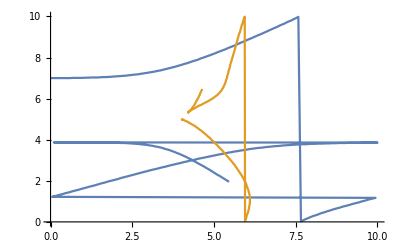

```mathematica
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Aula10_0510/Results/";
data = Import[path <> "Box.txt", "Data"];
n = 2;
ListLinePlot[Table[Table[{data[[i]][[2*p-1]],data[[i]][[2*p]]},{i, 1,Length[data]}],{p, 1,n}], ImageSize->Full, PlotRange->{{0,10},{0,10}}]
```